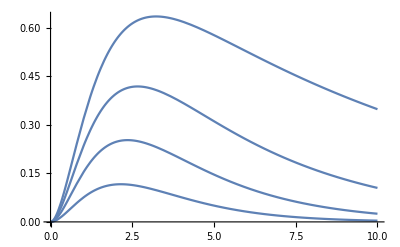

```mathematica
a=(2B)/(1+√(1-4B));
b=(2B)/(1-√(1-4B));
pfunc[B_]:=Plot[(E^(-(2B)/(1+√(1-4B)) x)-E^(-(2B)/(1-√(1-4B)) x))^2,{x,0,10}];
a1=pfunc[0.05];
a2=pfunc[0.1];
a3=pfunc[0.15];
a4=pfunc[0.2];
Show[{a1,a2,a3,a4}]
```

```mathematica
exa=Plot[{(E^(-(2 0.05)/(1+√(1-4 0.05)) x)-E^(-(2 0.05)/(1-√(1-4 0.05)) x))^2,(E^(-(2 0.1)/(1+√(1-4 0.1)) x)-E^(-(2 0.1)/(1-√(1-4 0.1)) x))^2,(E^(-(2 0.15)/(1+√(1-4 0.15)) x)-E^(-(2 0.15)/(1-√(1-4 0.15)) x))^2,(E^(-(2 0.2)/(1+√(1-4 0.2)) x)-E^(-(2 0.2)/(1-√(1-4 0.2)) x))^2},{x,0,10},PlotLabels->{"B=0.05","B=0.1","B=0.15","B=0.2"},Ticks->False];
Export["fig.pdf",exa]
```

fig.pdf